```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/andreaaparicio/Dropbox (Partners HealthCare)/ChanningN/Projects/Feasibility of MC/Code/channingReviewPackage/Fig1

```mathematica
At=Import["Asimst.csv"];
A=At⟦2;;11,2;;11⟧;
Cons=-At⟦2;;6,7;;⟧;
Zl = DiagonalMatrix[RandomReal[{0,Max[Cons]},5]];
Zs = Z*0.001;

minval = Min[Min[Zl], Min[Zs], Min[Cons]];
maxval = Max[Max[Zl], Max[Cons], Max[Zs]];
cf=If[#==0,White,Blend[{RGBColor["#fff6f0"], RGBColor["#f56200"]},Rescale[#,{minval,maxval}]]]&;
```

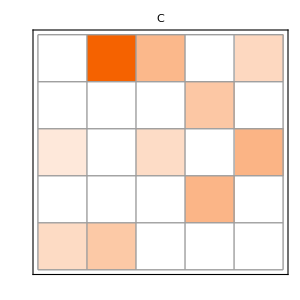

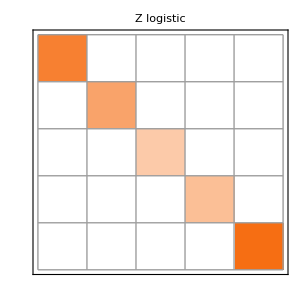

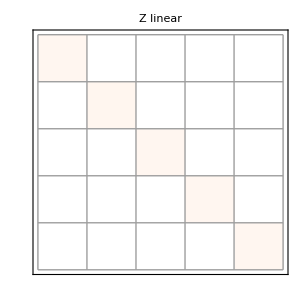

```mathematica
MatrixPlot[Transpose@Cons, ColorFunction -> cf, 
 ColorFunctionScaling -> False, 
 PlotLabel -> "C", ImageSize -> 300,PlotTheme->"Minimal",Mesh->All,PlotLegends-> Placed[Automatic,Below],LabelStyle->Directive[FontFamily->"Arial",FontSize->30]]

MatrixPlot[Zl, ColorFunction -> cf, 
 ColorFunctionScaling -> False, 
 PlotLabel -> "Z logistic", ImageSize -> 300,PlotTheme->"Minimal",Mesh->All,LabelStyle->Directive[FontFamily->"Arial",FontSize->30]]

MatrixPlot[Zs, ColorFunction -> cf, 
 ColorFunctionScaling -> False, 
 PlotLabel -> "Z linear", ImageSize -> 300,PlotTheme->"Minimal",Mesh->All,LabelStyle->Directive[FontFamily->"Arial",FontSize->30]]
```